```mathematica
"Multipole Single U - UHF-Uniform Heat Flux"
```

```mathematica
ClearAll["Global`*"]
```

```mathematica
temp=30;
Qi=Quantity[ 12./60000,("Meters"^3/"Seconds")] (*flow-rate[m^3/s]*); 
rpi=Quantity[0.0131,"Meters"] (*inner radius[m]*); 
rpo=Quantity[0.016,"Meters"] (*outer radius of pipe [m]*); 
kpipe=Quantity[0.38,("Watts"/("Meters"*"Kelvins"))] (*pipe thermal conductivity [W/(m.K)]*); 
kgrout=Quantity[1.2,("Watts"/("Meters"*"Kelvins"))] (*grout thermal conductivity [W/(m.K)]*); 
ss=Quantity[0.072,"Meters"] (*shank space [m]*); 
rb=Quantity[0.216/2,"Meters"](*borehole radius [m]*); 
Hb=Quantity[56,"Meters"] (*Borehole depth [m]*);
ks=Quantity[1.72,("Watts"/("Meters"*"Kelvins"))](*ground thermal conductivity [W/(m.K)]*);
```

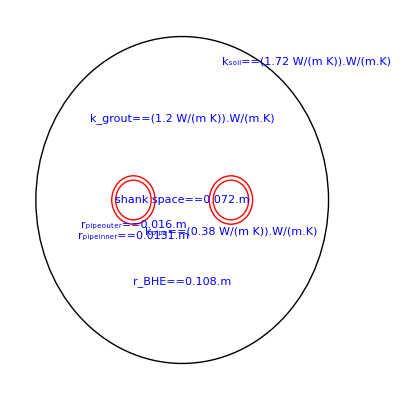

```mathematica
tempr=temp+273.15;
rhof=ThermodynamicData["Water","Density",{"Temperature"-> Quantity[tempr,"Kelvins"]}] (*fluid density[kg/m^3]*); 
mu=ThermodynamicData["Water","Viscosity",{"Temperature"-> Quantity[tempr,"Kelvins"]}](*dynamic viscosity [Pa.s]*); 
cpf0=ThermodynamicData["Water","IsobaricHeatCapacity",{"Temperature"-> Quantity[tempr,"Kelvins"]}](*fluid specific heat capacity [J/kgK]*); 
cpf=UnitConvert[cpf0]/."KelvinsDifference"->"Kelvins";
kfluid0=ThermodynamicData["Water","ThermalConductivity",{"Temperature"-> Quantity[tempr,"Kelvins"]}](*fluid thermal conductivity [W/(m.K)]*); 
kfluid=UnitConvert[kfluid0]/."KelvinsDifference"->"Kelvins";
rb1=QuantityMagnitude[rb];ss1=QuantityMagnitude[ss];rpo1=QuantityMagnitude[rpo];rpi1=QuantityMagnitude[rpi];rb1=QuantityMagnitude[rb];
 Graphics[{Circle[{0,0},rb1],{Red,Circle[{-ss1/2,0},rpo1],Circle[{ss1/2,0},rpo1],Circle[{ss1/2,0},rpi1],Circle[{-ss1/2,0},rpi1]},{Blue,Inset[Subscript[k, grout]==kgrout .(W/(m.K)),{0,rb1/2}],Inset[Subscript[k, soil]==ks .(W/(m.K)),{rb1*0.85,rb1*0.85}],Inset[Subscript[k, pipe]==kpipe .(W/(m.K)),{ss1/2,-rpo1*1.3}],Inset[Subscript[r, pipeinner]==rpi1 .(m),{-ss1/2,-rpi1*1.8}],Inset[Subscript[r, pipeouter]==rpo1.(m),{-ss1/2,-rpi1.5-0.01}],Inset[shank space==ss1.(m),{0,0}],Inset[Subscript[r, BHE]==rb1 .(m),{0,-rb1/2}]}}]
```

```mathematica
Vfluid=Qi/(π*rpi^2);
θ1=ss/(2*rb);
θ2=rb/rpo;
θ3=rpo/ss;
σ1=(kgrout-ks)/(kgrout+ks);
Rpc=1/(2*π*kpipe)*Log[rpo/rpi];
Re1=(rhof*Vfluid*2*rpi)/mu;
Pr=(cpf*mu)/kfluid;
ff=(0.79*Log[Re1]-1.64)^-2;
NUpi=((ff/8)*(Re1-1000)*Pr)/(1+12.7*(ff/8)^(1/2)*(Pr^(2/3)-1)) ; 
hpi=(NUpi*kfluid)/(2*rpi) ; 
Rpic=1/(2*π*rpi*hpi) ; 
Rp=Rpc+Rpic;
Beta1=2*π*kgrout*Rp;
Rb1U=1/(4*π*kgrout)(Beta1+Log[θ2/(2*θ1*(1-θ1^4)^σ1)]-(θ3^2*(1-(4*σ1*θ1^4)/(1-θ1^4))^2)/((1+Beta1)/(1-Beta1)+θ3^2*(1+(16*σ1*θ1^4)/((1-θ1^4)^2)))) ;
Ra1U=1/(π*kgrout)*(Beta1+Log[((1+θ1^2)^σ1)/(θ3*(1-θ1^2)^σ1)]-(θ3^2*(1-θ1^4+4*σ1*θ1^2)^2)/((1+Beta1)/(1-Beta1)*(1-θ1^4)^2-θ3^2*(1-θ1^4)^2+8*σ1^2*θ1^2*θ3^2*(1+θ1^4)));
Rbstar[te]=Rb1U+1/(3*Ra1U)*(Hb/(rhof*cpf*Qi))^2
```

0.200291 m K/W

### Thermal Resistance Change with Temperature

```mathematica
For[te=28,te<37,te++;
Qi=Quantity[ 12./60000,("Meters"^3/"Seconds")] (*flow-rate[m^3/s]*); 
rpi=Quantity[0.0131,"Meters"] (*inner radius[m]*); 
rpo=Quantity[0.016,"Meters"] (*outer radius of pipe [m]*); 
kpipe=Quantity[0.38,("Watts"/("Meters"*"Kelvins"))] (*pipe thermal conductivity [W/(m.K)]*); 
kgrout=Quantity[1.2,("Watts"/("Meters"*"Kelvins"))] (*grout thermal conductivity [W/(m.K)]*); 
ss=Quantity[0.072,"Meters"] (*shank space [m]*); 
rb=Quantity[0.108,"Meters"](*borehole radius [m]*); 
Hb=Quantity[56,"Meters"] (*Borehole depth [m]*);
ks=Quantity[1.72,("Watts"/("Meters"*"Kelvins"))](*ground thermal conductivity [W/(m.K)]*);
Which[ss/2+rpo>rb,"out of range"];
tempr=te+273.15;
rhof=ThermodynamicData["Water","Density",{"Temperature"-> Quantity[tempr,"Kelvins"]}] (*fluid density[kg/m^3]*); 
mu=ThermodynamicData["Water","Viscosity",{"Temperature"-> Quantity[tempr,"Kelvins"]}](*dynamic viscosity [Pa.s]*); 
cpf0=ThermodynamicData["Water","IsobaricHeatCapacity",{"Temperature"-> Quantity[tempr,"Kelvins"]}](*fluid specific heat capacity [J/kgK]*); 
cpf=UnitConvert[cpf0]/."KelvinsDifference"->"Kelvins";
kfluid0=ThermodynamicData["Water","ThermalConductivity",{"Temperature"-> Quantity[tempr,"Kelvins"]}](*fluid thermal conductivity [W/(m.K)]*); 
kfluid=UnitConvert[kfluid0]/."KelvinsDifference"->"Kelvins";
rb1=QuantityMagnitude[rb];ss1=QuantityMagnitude[ss];rpo1=QuantityMagnitude[rpo];rpi1=QuantityMagnitude[rpi];rb1=QuantityMagnitude[rb];
Vfluid=Qi/(π*rpi^2);
θ1=ss/(2*rb);
θ2=rb/rpo;
θ3=rpo/ss;
σ1=(kgrout-ks)/(kgrout+ks);
Rpc=1/(2*π*kpipe)*Log[rpo/rpi];
Re1=(rhof*Vfluid*2*rpi)/mu;
Pr=(cpf*mu)/kfluid;
ff=(0.79*Log[Re1]-1.64)^-2;
NUpi=((ff/8)*(Re1-1000)*Pr)/(1+12.7*(ff/8)^(1/2)*(Pr^(2/3)-1)) ; 
hpi=(NUpi*kfluid)/(2*rpi) ; 
Rpic=1/(2*π*rpi*hpi) ; 
Rp=Rpc+Rpic;
Beta1=2*π*kgrout*Rp;
Rb1U=1/(4*π*kgrout)(Beta1+Log[θ2/(2*θ1*(1-θ1^4)^σ1)]-(θ3^2*(1-(4*σ1*θ1^4)/(1-θ1^4))^2)/((1+Beta1)/(1-Beta1)+θ3^2*(1+(16*σ1*θ1^4)/((1-θ1^4)^2)))) ;
Ra1U=1/(π*kgrout)*(Beta1+Log[((1+θ1^2)^σ1)/(θ3*(1-θ1^2)^σ1)]-(θ3^2*(1-θ1^4+4*σ1*θ1^2)^2)/((1+Beta1)/(1-Beta1)*(1-θ1^4)^2-θ3^2*(1-θ1^4)^2+8*σ1^2*θ1^2*θ3^2*(1+θ1^4)));
Rbstar[te]=Rb1U+1/(3*Ra1U)*(Hb/(rhof*cpf*Qi))^2;]
```

```mathematica
Rbstar[#]&/@Range[29,35,1]
```

{0.200327 m K/W,0.200291 m K/W,0.200257 m K/W,0.200223 m K/W,0.200191 m K/W,0.20016 m K/W,0.20013 m K/W}

```mathematica
{#,QuantityMagnitude[Rbstar[#]]}&/@Range[29,35,1]
```

{{29,0.200327},{30,0.200291},{31,0.200257},{32,0.200223},{33,0.200191},{34,0.20016},{35,0.20013}}

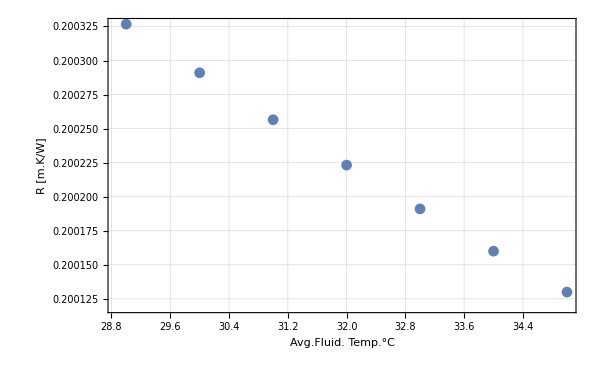

```mathematica
ListPlot[{#,QuantityMagnitude[Rbstar[#]]}&/@Range[29,35,1],PlotTheme->"Detailed",FrameLabel->{"Avg.Fluid. Temp.°C","R [m.K/W]"},ImageSize->600]
```